```mathematica
Needs["MFGraphs`"]
```

```mathematica
Names["MFGraphs`*"]
```

### Using the new functions in IterationFunction.m

```mathematica
Data=DataG[26];
MFGEquations=DataToEquations[Data];
```

Solving the linear equations

Done.

#### This is the reduction of the system (in place of Reduce)

```mathematica
reduced = FixedPoint[EqEliminatorX,{MFGEquations["EqAllAll"],{}},10]
```

{u61≤u61&&u61≤∞,{j49→80,j50→80,j51→80,j52→0,j53→0,j54→0,jt55→0,jt56→80,jt57→80,jt58→0,u59→u61,u60→15,u62→15,u63→15,u64→u61}}

```mathematica
EqEliminatorX[%]
```

{u61≤u61&&u61≤∞,{j49→80,j50→80,j51→80,j52→0,j53→0,j54→0,jt55→0,jt56→80,jt57→80,jt58→0,u59→u61,u60→15,u62→15,u63→15,u64→u61}}

```mathematica
EqEliminatorX[%]
```

{u61≤u61&&u61≤∞,{j49→80,j50→80,j51→80,j52→0,j53→0,j54→0,jt55→0,jt56→80,jt57→80,jt58→0,u59→u61,u60→15,u62→15,u63→15,u64→u61}}

#### The critical congestion case (general numeric solver)

```mathematica
startrulesX=StartSolverX[MFGEquations]
AssociateTo[MFGEquations,"CriticalCongestionSolution"->First[startrulesX]];
```

{{j49→80,j50→80,j51→80,j52→0,j53→0,j54→0,jt55→0,jt56→80,jt57→80,jt58→0,u59→95,u60→15,u61→95,u62→15,u63→15,u64→95}}

```mathematica
First @startrulesX
```

{j14→2,j15→1/2,j16→3/2,j17→1/2,j18→3/2,j19→2,j20→0,j21→0,j22→0,j23→0,j24→0,j25→0,jt26→0,jt27→2,jt28→1/2,jt29→3/2,jt30→0,jt31→0,jt32→0,jt33→0,jt34→1/2,jt35→0,jt36→3/2,jt37→0,u38→9/2,u39→5/2,u40→5/2,u41→2,u42→1,u43→9/2,u44→5/2,u45→2,u46→1,u47→2,u48→1,u49→9/2}

#### Non-linear case

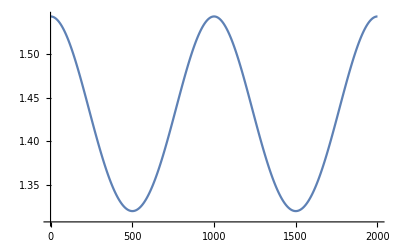

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

```mathematica
MFGEquations["Nrhs"]/.reduced[[2]]
```

{64.1073}

```mathematica
reduced[[2]]
```

{j49→80,j50→80,j51→80,j52→0,j53→0,j54→0,jt55→0,jt56→80,jt57→80,jt58→0,u59→u61,u60→15,u62→15,u63→15,u64→u61}

```mathematica
FixedPointSolverStepX[MFGEquations][{reduced[[2]]}]
```

95-u61==64.1073

95-u61==64.1073&&u61≤u61&&u61≤∞

ReplaceAll::reps: {95-u61==64.1073&&{j49==80,j50==80,j51==80,j52==0,j53==0,j54==0,«3»,jt58==0,u59==u61,u60==15,u62==15,u63==15,u64==u61}} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{95-u61==64.1073&&u61≤u61&&u61≤∞/.95-u61==64.1073&&{j49==80,j50==80,j51==80,j52==0,j53==0,j54==0,jt55==0,jt56==80,jt57==80,jt58==0,u59==u61,u60==15,u62==15,u63==15,u64==u61},95-u61==64.1073&&{j49==80,j50==80,j51==80,j52==0,j53==0,j54==0,jt55==0,jt56==80,jt57==80,jt58==0,u59==u61,u60==15,u62==15,u63==15,u64==u61}}

{j49→80,j50→80,j51→80,j52→0,j53→0,j54→0,jt55→0,jt56→80,jt57→80,jt58→0,u59→u61,u60→15,u62→15,u63→15,u64→u61}